# Лабораторная работа 3. Основы работы с графикой.

Выполнила студентка ММФ БГУ
  1 к, 5 гр. Шклярик В.С.
21 ноября 2021

## Задание 1. Графическое изображение треугольника.

```mathematica
ClearAll[points];
Partition[Table[RandomInteger[{-4,6}],6],2]
```

{{0,2},{0,-1},{-4,-3}}

```mathematica
points={{3,0},{-2,2},{0,-4}}
```

{{3,0},{-2,2},{0,-4}}

```mathematica
Graphics[{FaceForm[White],EdgeForm[Directive[Thick,Black]],Polygon[points]},ImageSize->100,AspectRatio->Automatic]
```

-Graphics-

```mathematica
ClearAll[G,f,g,vect,vectNormal,vectLength,vectCross];
vect[{A_,B_}]:=B-A;
vectNormal[{A_,B_}]:={1,-1}*vect[{A,B}]//Reverse;
vectLength[{A_,B_}]:=√(#.#)&[B-A];
vectCross[{A_,B_},{C_,D_}]:=vectLength[{A,B}]*vectLength[{C,D}]*Sin[VectorAngle[vect[{A,B}],vect[{C,D}]]];
```

Создадим некоторые функции для работы с векторами.
vect по заданным координатам начала и конца вектора получает координаты вектора, vectNormal по заданным координатам начала и конца направляющего вектора прямой получает координаты вектора-нормали к прямой, vectLength по заданным координатам начала и конца вектора находит его длину, vectCross находит векторное произведение двух векторов, каждый из которых задан списком координат начала и конца вектора.

```mathematica
vectLength[{points⟦2⟧,points⟦3⟧}]
```

2 √10

Функция triangle по заданному списку координат вершин треугольника создает графический объект для отображения треугольника. Также проверяется, существует ли треугольник, образованный заданными точками.

```mathematica
ClearAll[triangle];
triangle[pts_List]:={FaceForm[White],EdgeForm[Directive [Thick,Black]],Polygon[pts],{Red,AbsolutePointSize[6],Point[#]&/@pts},MapThread[Text[#1,#2]&,{{"A","B","C"},pts+0.2}]}/;vectCross[Most@pts,Rest@pts]≠0
```

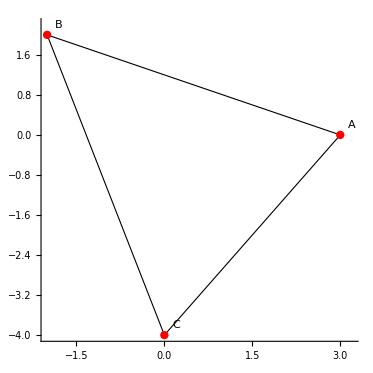

```mathematica
Graphics[triangle[points],Axes->True,AspectRatio->1]
```

## Задание 2. Нахождение площади треугольника.

Функция s находит величину площади треугольника по заданному списку координат вершин треугольника.

```mathematica
ClearAll[s];
s[pts_List]:=1/2*vectCross[Most@pts,Rest@pts];
```

```mathematica
s[points]
```

13

## Задание 3. Отображение медианы треугольника.

Функция findMedian по заданному списку координат вершин треугольника(первый аргумент) и координатам вершины, из которой опущена медиана(второй аргумент) вычисляет координаты начала и конца искомой медианы.
Функция median  по заданному списку координат вершин треугольника(первый аргумент) и координатам вершины, из которой опущена медиана(второй аргумент) строит графический объект Line для отображения отрезка медианы, а также графический объект Point для отображения основания медианы.

```mathematica
ClearAll[median,findMedian];
findMedian[pts_List,vertex_]:={vertex,1/2*Plus@@(DeleteCases[pts,vertex])};
median[pts_List,vertex_]:={Green,Line[#],PointSize[0.03],Point[#//Last]}&/@{findMedian[pts,vertex]};
```

```mathematica
findMedian[points,points⟦1⟧]
```

{{3,0},{-1,-1}}

```mathematica
median[points,points⟦1⟧]
```

{{RGBColor[0, 1, 0],Line[{{3,0},{-1,-1}}],PointSize[0.03],Point[{-1,-1}]}}

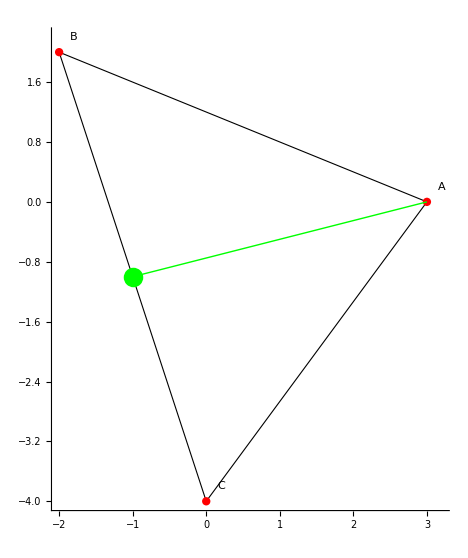

```mathematica
Graphics[{triangle[points],  median[points,points⟦1⟧]},Axes->True,AspectRatio->Automatic]
```

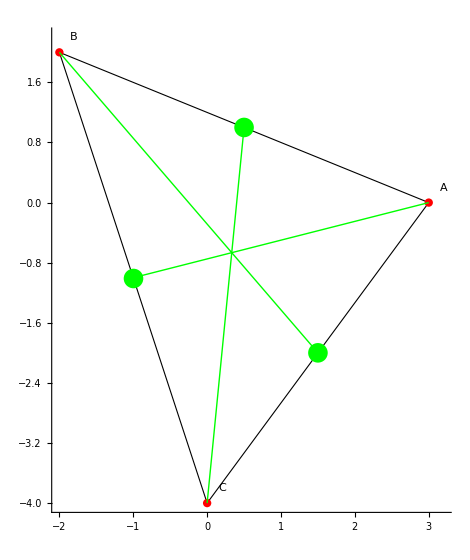

```mathematica
Graphics[{triangle[points],  median[points,points⟦#⟧]&/@{1,2,3}},Axes->True,AspectRatio->Automatic]
```

## Задание 4. Отображение высоты.

Вспомогательная функция equation по заданным координатам точки(первый аргумент) и координатам направляющего вектора прямой(второй аргумент) строит уравнение прямой.
Функция findAttitude по заданному списку координат вершин треугольника(первый аргумент) и координатам вершины, из которой опущена высота(второй аргумент) вычисляет координаты начала и конца высоты.

```mathematica
ClearAll[y,x,equation,findAttitude];
equation[point_List,vector_List]:=(x-point⟦1⟧)*vector⟦2⟧==(y-point⟦2⟧)*vector⟦1⟧;
findAttitude[pts_List,vertex_]:=Module[{base=DeleteCases[pts,vertex]},{vertex,({x,y}/.Solve[{equation[vertex,vectNormal[base]],equation[base//First,vect[base]]},{x,y}])//Flatten}];
```

```mathematica
findAttitude[points,points⟦1⟧]
```

{{3,0},{-9/10,-13/10}}

Функция attitude по заданному списку координат вершин треугольника(первый аргумент) и координатам вершины, из которой опущена высота(второй аргумент) создает графический объект Line для отображения отрезка высоты, а также графический объект Point для отображения основания высоты.

```mathematica
ClearAll[attitude];
attitude[pts_List,vertex_]:={Blue,Line[findAttitude[pts,vertex]],PointSize[0.03],Point[findAttitude[pts,vertex]//Last]}
```

```mathematica
attitude[points,points⟦1⟧]
```

{RGBColor[0, 0, 1],Line[{{3,0},{-9/10,-13/10}}],PointSize[0.03],Point[{-9/10,-13/10}]}

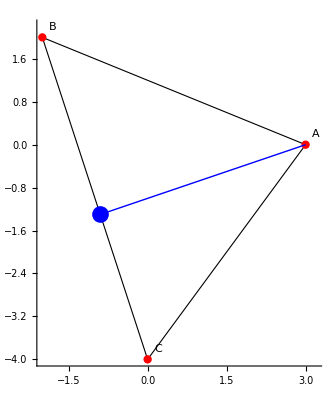

```mathematica
Graphics[{triangle[points],attitude[points,points⟦1⟧]},Axes->True,AspectRatio->Automatic]
```

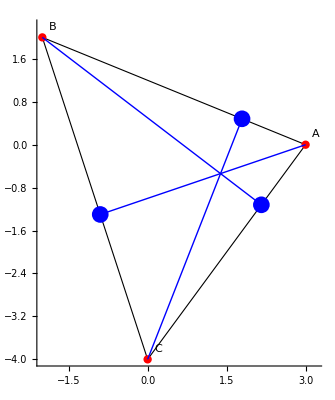

```mathematica
Graphics[{triangle[points],attitude[points,points⟦#⟧]&/@{1,2,3}},Axes->True,AspectRatio->Automatic]
```

## Задание 5. Отображение биссектрисы треугольника.

Функция findBissectris по заданному списку координат вершин треугольника(первый аргумент) и координатам вершины, из которой опущена биссектриса(второй аргумент) вычисляет координаты начала и конца биссектрисы. Используется описанная ранее вспомогательная функция equation.

```mathematica
ClearAll[findBissectris];
findBissectris[pts_,vertex_]:=Module[{base=DeleteCases[pts,vertex],dirVect=Plus[vect[#1]/vectLength[#1],vect[#2]/vectLength[#2]]&[{vertex,DeleteCases[pts,vertex]//First},{vertex,DeleteCases[pts,vertex]//Last}]},{vertex,({x,y}/.Solve[{equation[vertex,dirVect],equation[base//First,vect[base]]},{x,y}])//Flatten}];
```

```mathematica
findBissectris[points,points⟦1⟧]
```

{{3,0},{-(10 √29)/(29+5 √29),(2 (-58+5 √29))/(29+5 √29)}}

Функция bissectris по заданному списку координат вершин треугольника(первый аргумент) и координатам вершины, из которой опущена биссектриса(второй аргумент) создает графический объект Line для отображения отрезка биссектрисы, а также графический объект Point для отображения основания биссектрисы.

```mathematica
ClearAll[bissectris];
bissectris[points_,vertex_]:={Pink,Line[findbisectriss[points,vertex]],PointSize[0.03],Point[findbisectriss[points,vertex]//Last]}
```

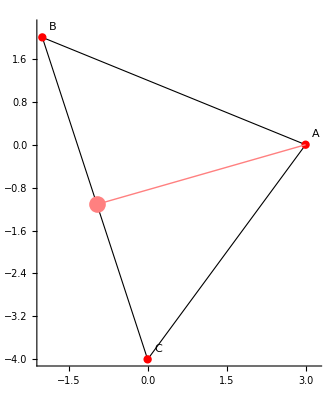

```mathematica
Graphics[{triangle[points],bissectris[points,points⟦1⟧]},Axes->True]
```

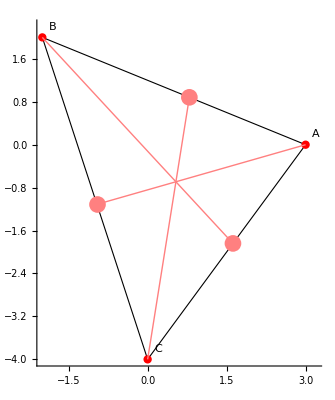

```mathematica
Graphics[{triangle[points],bissectris[points,points⟦#⟧]&/@{1,2,3}},Axes->True]
```

## Задание 6. Отображение описанной окружности треугольника.

Функция radiusR по заданному списку координат вершин треугольника находит величину радиуса описанной около данного треугольника окружности.

```mathematica
ClearAll[radiusR];
radiusR[pts_List]:=Module[{list=Partition[Flatten[{pts,pts},1],2]},(Times@@(vectLength[#]&/@list))/(4 s[pts])];
```

```mathematica
radiusR[points]
```

(5 √(145/2))/13

Вспомогательная функция equationR по заданному списку координат вершин треугольника(первый аргумент) и величине радиуса описанной окружности треугольника(второй аргумент) строит уравнение окружности, описанной около данного треугольника.
Функция centerCoordsR по заданному списку координат вершин треугольника находит координаты центра окружности, описанной около данного треугольника.

```mathematica
ClearAll[centerCoords,centerCoordsR];
equationR[pts_List,R_]:=(pts⟦1⟧-a)^2+(pts⟦2⟧-b)^2==R^2;
centerCoordsR[pts_List]:=Block[{a,b},Flatten[({a,b}/.Solve[MapThread[equationR,{pts⟦#⟧&/@{1,2,3},Table[radiusR[pts],3]}],{a,b}])]];
```

Функция outCircle по заданному списку координат вершин треугольника строит графический объект Circle для отображения окружности, описанной около заданного треугольника.

```mathematica
outCircle[pts_List]:={Orange,Circle[centerCoordsR[pts],radiusR[pts]]};
```

```mathematica
centerCoordsR[points]
```

{-5/26,-19/26}

```mathematica
outCircle[points]
```

{RGBColor[1, 0.5, 0],Circle[{-5/26,-19/26},(5 √(145/2))/13]}

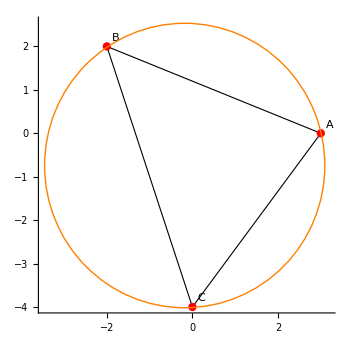

```mathematica
Graphics[{triangle[points],outCircle[points]},Axes->True,AspectRatio->Automatic]
```

## Задание 7. Отображение вписанной окружности треугольника.

Функция radiusr по заданному списку координат вершин треугольника находит величину радиуса вписанной окружности данного треугольника.

```mathematica
ClearAll[radiusr];
radiusr[pts_List]:= Module[{list=Partition[Flatten[{pts,pts},1],2]},(2 s[pts])/(Plus@@(vectLength[#]&/@list))];
```

```mathematica
radiusr[points]
```

26/(5+2 √10+√29)

Вспомогательная функция equationr по заданному списку координат двух точек строит уравнение прямой, проходящей через данные точки.
Функция centerCoordsr по заданному списку координат вершин треугольника находит координаты центра вписанной в заданный треугольник окружности.

```mathematica
ClearAll[centerCoordsr,equationr];
equationr[{point1_List,point2_List}]:=((#2⟦2⟧-#1⟦2⟧)*(a-#1⟦1⟧)-(#2⟦1⟧-#1⟦1⟧)*(b-#1⟦2⟧))&[point1,point2]==0;
centerCoordsr[pts_List]:=Flatten[{a,b}/.Solve[equationr[findBissectris[pts,pts⟦#⟧]]&/@{1,2,3},{a,b}]];
```

```mathematica
centerCoordsr[points]
```

{-(10 (-6 √29+√290))/(29 √10+20 √29+5 √290),(2 (-58 √10+5 √290))/(29 √10+20 √29+5 √290)}

Функция inCircle по заданному списку координат вершин треугольника строит графический объект Circle для отображение окружности, вписанной в данный треугольник.

```mathematica
inCircle[pts_List]:={Cyan,Circle[centerCoordsr[pts],radiusr[pts]]};
```

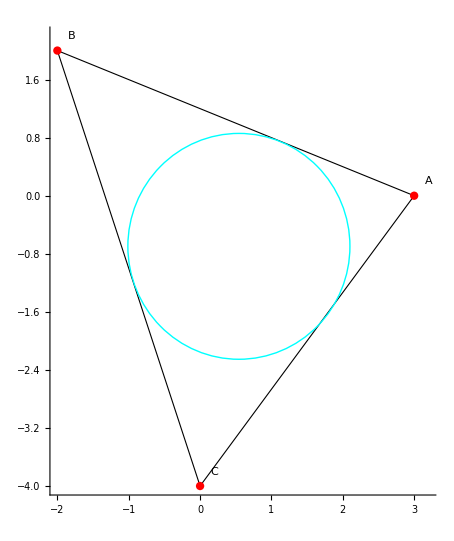

```mathematica
Graphics[{triangle[points],inCircle[points]},Axes->True,AspectRatio->Automatic]
```

## Задание 8. Создание пользовательского интерфейса.

Функция myInterface по заданному списку координат вершин треугольника создает интерактивный объект для управления отображением вписанной и описанной окружностей данного треугольника, а также медианы, высоты, биссектрисы, опущенных из любой вершины треугольника, в зависимости от выбранных параметров.

```mathematica
ClearAll[myInterface,MyInterface];
myInterface[pts_List]:=Manipulate[Graphics[{triangle[pts],Blue,Text[s[pts]//N,{1,2}],f[pts,pts[[i]]],If[t,outCircle[pts]],If[z,inCircle[pts]]},Axes->True,AspectRatio->Automatic],{f,{median,attitude,bisectriss}},{i,{1->"A",2->"B",3->"C"}},{{t,False,"outCircle"},{True,False}},{{z,False,"inCircle"},{True,False}}];
```

```mathematica
myInterface[points]
```